```mathematica
K[s_,m_]:=(2(m+1)^2*(m-s))/((2*m-1)*m^2)
L[s_,m_]:=(m+s+1)/(2*m+3)
```

```mathematica
NN[s_,m_,y_]:=2*((m+1)/m-s/m^2*1/y)
```

```mathematica
M[s_,m_,y_,x_]:=2*((y)^2*((m+1)/m-s/m^2*1/y)-(m+1)^2*x^2)
```

```mathematica
s=2;
T=24*3600;
omega=2*π/T;
g=9.8;
R=6.37*10^6;
```

```mathematica
h=(2*omega*R)^2/g
```

87588.1

```mathematica
matrixGenerator[s_,m_,y_,x_]:=
Module[{Matrix,aa,bb,cc},
cc=Table[L[s,i],{i,2,m}];
bb=Table[If[EvenQ[i],-M[s,i,y,x],-NN[s,i,y]],{i,2,m+1}];
aa=Table[K[s,i],{i,3,m+1}];
Matrix=SparseArray[{Band[{1,2}]->cc,Band[{1,1}]->bb,Band[{2,1}]->aa},m]
]
```

```mathematica
MatrixForm[matrixGenerator[s,7,1,1]]
```

(16 | 5/7 | 0 | 0 | 0 | 0 | 0
32/45 | -20/9 | 2/3 | 0 | 0 | 0 | 0
0 | 25/28 | 191/4 | 7/11 | 0 | 0 | 0
0 | 0 | 24/25 | -56/25 | 8/13 | 0 | 0
0 | 0 | 0 | 98/99 | 862/9 | 3/5 | 0
0 | 0 | 0 | 0 | 640/637 | -108/49 | 10/17
0 | 0 | 0 | 0 | 0 | 81/80 | 2557/16)

```mathematica
h=(2*omega*R*x)^2/g;
```

87588.1 x^2

```mathematica
ListLinePlot[Table[Det[matrixGenerator[2,20,y,2]],{y,0.001,1,0.01}],DataRange->{0.001,1},PlotRange->Automatic]
```

-Graphics-

```mathematica
ListPlot[Table[Det[matrixGenerator[2,30,y,0.3]],{y,0.001,5,0.01}],DataRange->{0.001,5},PlotRange->Automatic]
Newtonian Method
```

-Graphics-

```mathematica
list={{{0.01,0.337},{0.05,0.705},{0.1,1},{0.5,5.25},{1,9.52},{1.2,12.6}},{{0.01,0.285},{0.05,0.63},{0.1,0.845},{0.5,4.285},{1,8.5},{1.2,10.2}},{{0.01,0.231},{0.05,0.53},{0.1,0.71},{0.5,3.3},{1,6.51},{1.2,7.8}},{{0.01,0.161},{0.05,0.38},{0.1,0.55},{0.5,2.33},{1,4.52},{1.2,5.4}},{{0.01,0.02},{0.05,0.09},{0.1,0.155},{0.5,1.43},{1,2.6},{1.2,3.15}}}
```

{{{0.01,0.337},{0.05,0.705},{0.1,1},{0.5,5.25},{1,9.52},{1.2,12.6}},{{0.01,0.285},{0.05,0.63},{0.1,0.845},{0.5,4.285},{1,8.5},{1.2,10.2}},{{0.01,0.231},{0.05,0.53},{0.1,0.71},{0.5,3.3},{1,6.51},{1.2,7.8}},{{0.01,0.161},{0.05,0.38},{0.1,0.55},{0.5,2.33},{1,4.52},{1.2,5.4}},{{0.01,0.02},{0.05,0.09},{0.1,0.155},{0.5,1.43},{1,2.6},{1.2,3.15}}}

```mathematica
For[y=0.1,y<0.7,y=y+0.00001,If[Abs[Det[matrixGenerator[2,32,y,x]]]<0.00000001,Print[y]]]
```

$Aborted

```mathematica
For[y=0.1,y<0.7,y=y+0.00001,If[Abs[Det[matrixGenerator[2,31,y,omega,x,g,R]]]<0.00000001,Print[y]]]
```

```mathematica
For[y=0.1,y<1,y=y+0.000001,If[Abs[Det[matrixGenerator[2,20,y,omega,0.05,g,R]]]<0.0001,Print[y]]]
```

```mathematica
For[y=0.5,y≤1.2,y=y+0.00001,If[Abs[Det[matrixGenerator[2,10,y,omega,0.1,g,R]]]<0.001,Print[y]]]
```

```mathematica
For[y=1,y≤5,y=y+0.00001,If[Abs[Det[matrixGenerator[2,3,y,omega,0.5,g,R]]]<0.01,Print[y]]]
```

```mathematica
For[y=1.1,y≤11,y=y+0.00001,If[Abs[Det[matrixGenerator[2,3,y,omega,1,g,R]]]<0.1,Print[y]]]
```

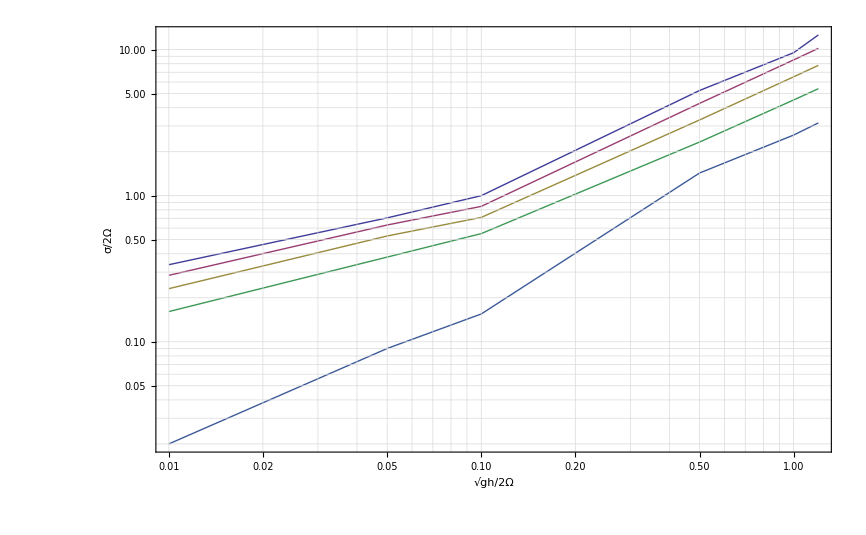

```mathematica
plot=ListLogLogPlot[list,FrameLabel->{"√gh/2Ω","σ/2Ω"},Joined->True,GridLines->Automatic,Frame->True]
```

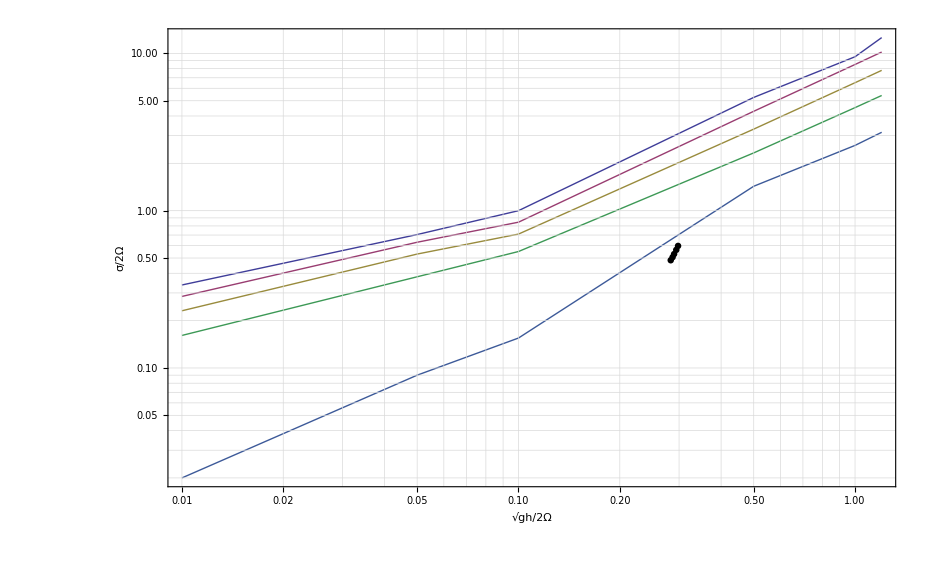

```mathematica
plot2=Show[plot,Graphics[{PointSize[0.005],Point[{{Log[0.29],Log[0.53]},{Log[0.297932],Log[0.597]},{Log[0.2943],Log[0.5634]},{Log[0.287],Log[0.506]},{Log[0.2834],Log[0.484]}}]}]]
```

```mathematica
(1367/(5.67*10^-8)/4)^(0.25)
```

278.632

```mathematica
h = 7400
```

7400

```mathematica
x0 = √(9.8*h)/(2 omega*R)
```

0.290665

```mathematica
sigma=2π/(22.6*3600);
```

```mathematica
y0=sigma/(2*omega)
```

0.530973

```mathematica
x1=x0-x0*0.2/8
```

0.283399

```mathematica
sigma1=2π/(24.8*3600);
```

```mathematica
y1=sigma1/(2*omega)
```

0.483871

```mathematica
omega
```

π/43200

```mathematica
h=300^2/9.8
```

9183.67

```mathematica
√(g*h)/(2*omega*R)
```

0.323807

```mathematica
ListPlot[Table[Det[matrixGenerator[2,40,y,0.324]],{y,0.001,5,0.01}],DataRange->{0.001,5},PlotRange->Automatic]
```

-Graphics-

```mathematica
sig=1.1*2*omega
```

0.000159989

```mathematica
2π/sig/3600
```

10.9091

```mathematica
N[2π/(omega*3600)]
```

24.

```mathematica
√0.1
```

0.316228

```mathematica
FindPeak
```

```mathematica
NormalDistribution
```

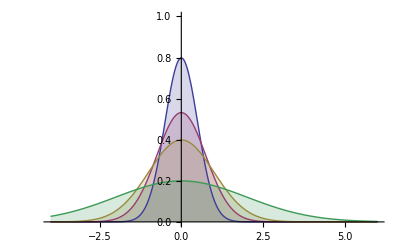

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,{0.5,.75,1,2}}],{x,-4,6},Filling->Axis,PlotRange->{0,1}]
```

```mathematica
PDF[NormalDistribution[0,0.5]]
```

Exp[-1/2 ((#1-0)/0.5)^2]/(0.5 √(2 π))&